```mathematica
ap[f_]:=(f*x+D[f,x])/Sqrt[2]
```

```mathematica
eq=ap[v[x]]==0
```

(x v[x]+v'[x])/(√2)==0

```mathematica
s1=DSolve[eq,v[x],x]
```

{{v[x]→ⅇ^(-x^2/2) C[1]}}

```mathematica
vv=v[x]/.s1[[1]]
```

ⅇ^(-x^2/2) C[1]

```mathematica
eq2=Integrate[vv^2,{x,-Infinity,Infinity}]==1
```

√π C[1]^2==1

```mathematica
sss=Solve[eq2,C[1]]
```

{{C[1]→-1/π^(1/4)},{C[1]→1/π^(1/4)}}

```mathematica
psi[0]=vv/.sss[[2]]
```

(ⅇ^(-x^2/2))/π^(1/4)

```mathematica
am[f_]:=(f*x-D[f,x])/Sqrt[2]
```

```mathematica
psi[n_]:=Together@am[psi[n-1]/√n]
```

```mathematica
psi[10]
```

(ⅇ^(-x^2/2) (-945+9450 x^2-12600 x^4+5040 x^6-720 x^8+32 x^10))/(720 √7 π^(1/4))

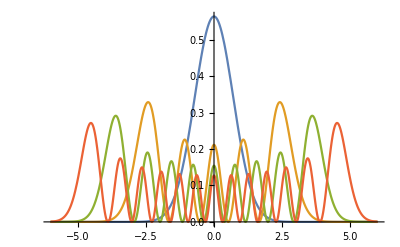

```mathematica
Plot[Evaluate@Table[psi[n]^2,{n,0,12,4}],{x,-6,6}]
```